```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/DEFECTIVE_FRENKEL"];
filesEin={"190modein", "191modein", "192modein"};
filesMol={"190modmol", "191modmol", "192modmol"};
filesPhon={"190modphon", "191modphon", "192modphon"};
dataEin=Table[ReadList[filesEin[[i]],{Number, Number}],{i,1,3}];
dataMol=Table[ReadList[filesMol[[i]],{Number, Number}],{i,1,3}];
dataPhon=Table[ReadList[filesPhon[[i]],{Number, Number}],{i,1,3}];
eVcell2meVatom=1000/64
```

125/8

```mathematica
dataEin
```

{{{1,-666.401},{2,-666.723},{3,-667.031},{4,-667.371},{5,-667.81},{6,-668.418},{7,-669.215},{8,-670.115},{9,-671.007},{10,-671.402},{11,-671.73},{12,-671.956},{13,-672.026},{14,-672.041},{15,-672.026},{16,-671.943},{17,-671.621},{18,-671.037},{19,-670.157},{20,-667.428},{21,-663.372},{22,-658.056},{23,-651.512},{24,-643.467},{25,-632.673},{26,-614.529},{27,-583.689}},{{1,-419.726},{2,-538.283},{3,-593.159},{4,-625.274},{5,-643.722},{6,-654.934},{7,-662.246},{8,-666.995},{9,-669.969},{10,-670.922},{11,-671.565},{12,-671.927},{13,-672.023},{14,-672.041},{15,-672.024},{16,-671.939},{17,-671.661},{18,-671.246},{19,-670.738},{20,-669.603},{21,-668.582},{22,-667.851},{23,-667.376},{24,-667.043},{25,-666.587},{26,-665.473},{27,-662.544}},{{1,-641.785},{2,-600.222},{3,-532.226},{4,-478.817},{5,-504.306},{6,-576.098},{7,-632.179},{8,-658.857},{9,-668.443},{10,-670.371},{11,-671.397},{12,-671.893},{13,-672.018},{14,-672.041},{15,-672.018},{16,-671.893},{17,-671.397},{18,-670.371},{19,-668.443},{20,-658.857},{21,-632.179},{22,-576.099},{23,-504.306},{24,-478.817},{25,-532.226},{26,-600.222},{27,-641.785}}}

```mathematica
Table[i,{i,-50,50,5}];
amps={-50,-45,-40,-35,-30,-25,-20,-15,-10,-7.5,-5,-2.5,-1,0,1,2.5,5,7.5,10,15,20,25,30,35,40,45,50}
amps//Length
```

{-50,-45,-40,-35,-30,-25,-20,-15,-10,-7.5,-5,-2.5,-1,0,1,2.5,5,7.5,10,15,20,25,30,35,40,45,50}

27

```mathematica
refEin=Table[Transpose[{amps,1000*(Transpose[dataEin[[i]]][[2]]-Transpose[dataEin[[i]]][[2]][[14]])}],{i,1,3}];
refMol=Table[Transpose[{amps,1000*(Transpose[dataMol[[i]]][[2]]-Transpose[dataMol[[i]]][[2]][[14]])}],{i,1,3}];
refPhon=Table[Transpose[{amps,1000*(Transpose[dataPhon[[i]]][[2]]-Transpose[dataPhon[[i]]][[2]][[14]])}],{i,1,3}];
```

15

5000

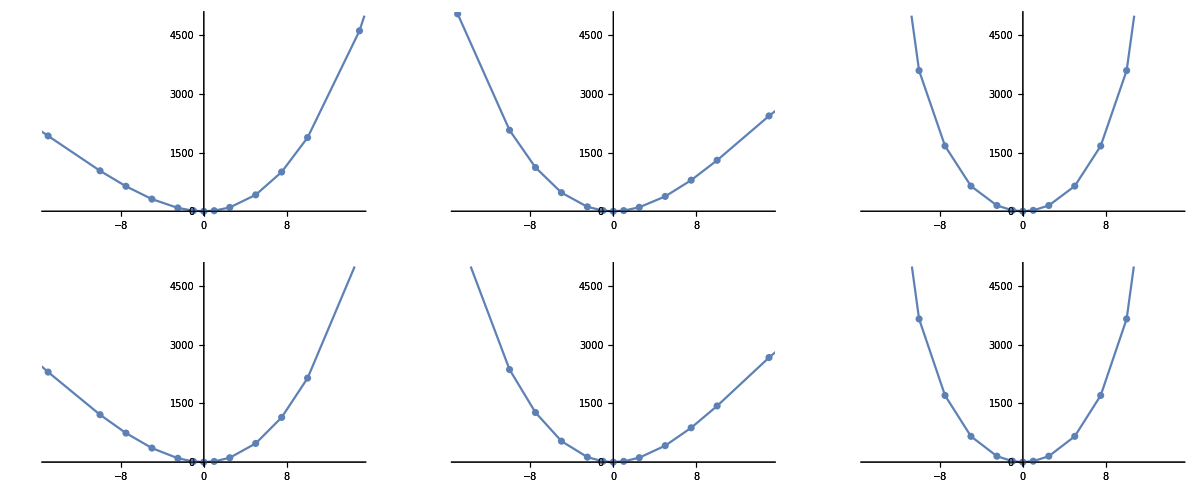

```mathematica
(*Show[GraphicsGrid[{Table[ListPlot[dataEin[[i]],Joined->True],{i,1,3}],Table[ListPlot[dataMol[[i]],Joined->True],{i,1,3}],Table[ListPlot[dataPhon[[i]],Joined->True],{i,1,3}]},ImageSize->1200],GraphicsGrid[{Table[ListPlot[dataEin[[i]]],{i,1,3}],Table[ListPlot[dataMol[[i]]],{i,1,3}],Table[ListPlot[dataPhon[[i]]],{i,1,3}]},ImageSize->1200]]*)
bound=15
bound2=5000
Show[GraphicsGrid[{Table[ListPlot[refEin[[i]],Joined->True,PlotRange->{{-bound,bound},{0,bound2}}],{i,1,3}],Table[ListPlot[refPhon[[i]],Joined->True,PlotRange->{{-bound,bound},{0,bound2}}],{i,1,3}]},ImageSize->1200],GraphicsGrid[{Table[ListPlot[refEin[[i]],PlotRange->{{-bound,bound},{0,bound2}}],{i,1,3}],Table[ListPlot[refPhon[[i]],PlotRange->{{-bound,bound},{0,bound2}}],{i,1,3}]},ImageSize->1200]]
```

```mathematica
refEin[[1]][[8;;20]]
```

{{-15,1926.02},{-10,1034.18},{-7.5,638.33},{-5,310.74},{-2.5,85.02},{-1,14.47},{0,0.},{1,14.73},{2.5,97.52},{5,419.26},{7.5,1003.78},{10,1884.04},{15,4613.01}}

```mathematica
b1=8;b2=20;
refEin[[1]][[13;;15]]
refEin[[1]][[b1;;b2]]
VD[1,1,x_]:=Table[Fit[refEin[[i]][[13;;15]],{x^2},x],{i,1,3,1}]
VD[1,2,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2},x],{i,1,3,1}]
VD[1,3,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3},x],{i,1,3,1}]
VD[1,4,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4},x],{i,1,3,1}]
VD[1,5,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4,x^5},x],{i,1,3,1}]
VD[1,6,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4,x^5,x^6},x],{i,1,3,1}]
VD[1,7,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4,x^5,x^6,x^7},x],{i,1,3,1}]
VD[1,8,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x],{i,1,3,1}]
VD[1,9,x_]:=Table[Fit[refEin[[i]][[b1;;b2]],{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x],{i,1,3,1}]
pots=Table[VD[1,i,x],{i,1,9,1}];
```

{{-1,14.47},{0,0.},{1,14.73}}

{{-15,1926.02},{-10,1034.18},{-7.5,638.33},{-5,310.74},{-2.5,85.02},{-1,14.47},{0,0.},{1,14.73},{2.5,97.52},{5,419.26},{7.5,1003.78},{10,1884.04},{15,4613.01}}

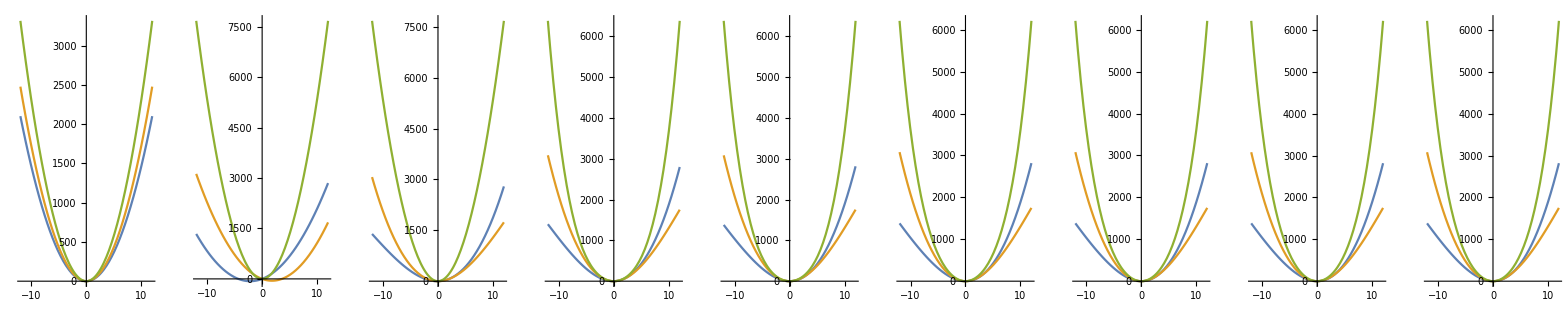

```mathematica
GraphicsGrid[{Table[Plot[Evaluate@pots[[i]],{x,-12,12},PlotRange->All],{i,1,9}]},ImageSize->2500]
```

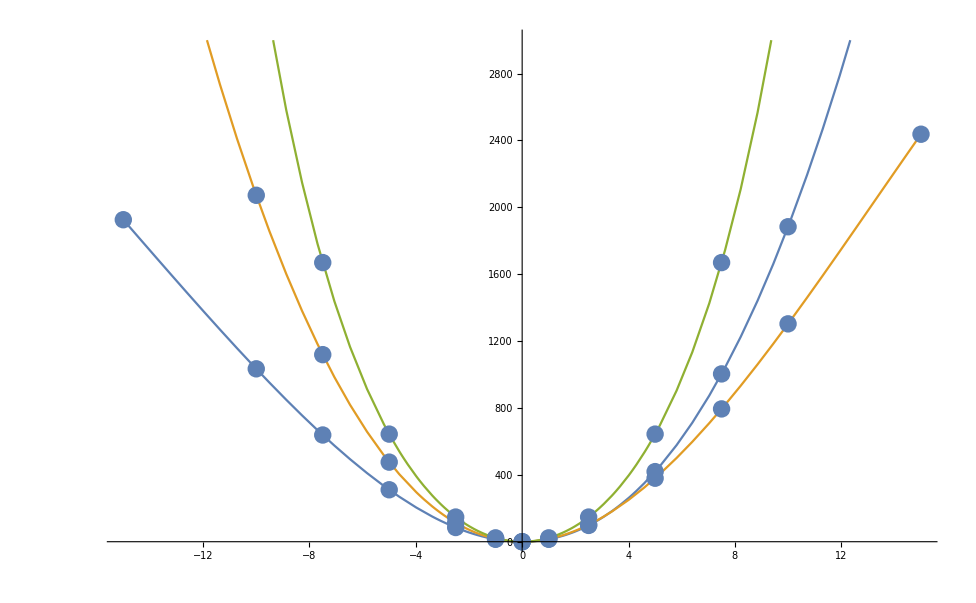

```mathematica
Show[Show[Plot[Evaluate@pots[[9]],{x,-15,15},PlotRange->{Automatic,{0,3000}}]],Show[Table[ListPlot[refEin[[i]]],{i,1,3}]]]
```

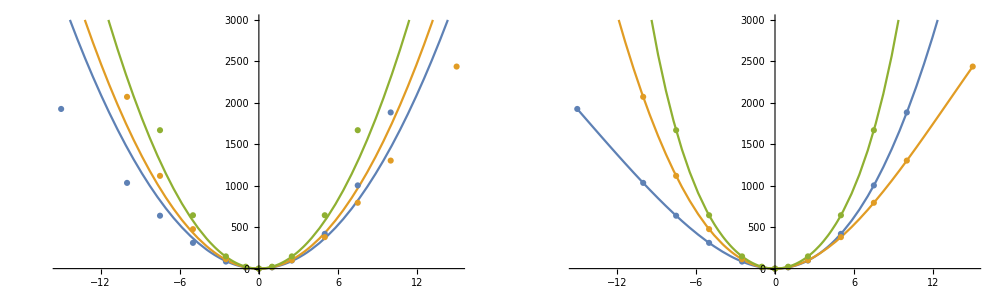

```mathematica
GraphicsGrid[{Table[Show[Plot[Evaluate@pots[[i]],{x,-15,15},PlotRange->{Automatic,{0,3000}}],ListPlot[refEin]],{i,1,9,8}]},ImageSize->1000]
```

```mathematica
eigenFactor=0.6(*Assuming three atoms are active in the vibration*)
amp=1
Natms=64
(amp/(Sqrt[m[[2]]Natms]))*eigenFactor
((Sqrt[m[[2]]Natms]))*eigenFactor
```

0.6

1

64

0.00785248

45.8454

```mathematica
64*Sqrt[m[[1]]*m[[2]]]
Sqrt[m[[1]]]
```

2118.45

3.46565

```mathematica
Frenkel defect - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=250;
(*Define bounds for plotting and solving eigenproblem*)
B=15;H=2000;
(*Carbon defect Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒalld=Table[Table[-(1/(2))*u''[x]+VD[1,order,x][[mode]]*u[x],{order,1,9,8}],{mode,1,3}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
(*omega_0=Sqrt[k/m]=Sqrt[2A/m]*)
(*In normal mode coordinates : -0.5nabla[q]+0.5*omega0^2q^2 *)
VD[1,1,x]
{Sqrt[2*VD[1,1,x][[1]][[1]]],Sqrt[2*VD[1,1,x][[2]][[1]]],Sqrt[2*VD[1,1,x][[3]][[1]]]}
{m[[1]]*Sqrt[2*VD[1,1,x][[1]][[1]]],m[[1]]*Sqrt[2*VD[1,1,x][[2]][[1]]],m[[1]]*Sqrt[2*VD[1,1,x][[3]][[1]]]}
```

{14.6 x^2,17.21 x^2,23.03 x^2}

{5.4037,5.86686,6.78675}

{64.9022,70.465,81.5136}

```mathematica
{94,102,113}/{5.403702434437536,5.8668560575548705,6.786751800375318}
```

{17.3955,17.3858,16.6501}

```mathematica
17.395480439659764^2
```

302.603

```mathematica
Sqrt[32*m[[1]]]//N
```

19.6047

```mathematica
Sqrt[m[[1]]]
Sqrt[m[[2]]]
Sqrt[m[[1]]]*Sqrt[m[[2]]]
Sqrt[64*Sqrt[m[[1]]]*Sqrt[m[[2]]]]
```

3.46565

9.55113

33.1008

46.0266

```mathematica
17.395480439659764*2
```

34.791

```mathematica
(*ℒalld[[fitOrder (harmonic|9thorder)]][[mode 190 191 192]]*)
Table[Table[ℒalld[[j]][[i]],{i,1,2}],{j,1,3}]//TableForm
```

14.6 x^2 u[x]-u''[x]/2 | (-0.326431 x+14.604 x^2+0.454115 x^3-0.000191967 x^4-0.000287568 x^5+1.60476×10^-6 x^6+3.50772×10^-7 x^7-9.73188×10^-9 x^8-6.71283×10^-10 x^9) u[x]-u''[x]/2
17.21 x^2 u[x]-u''[x]/2 | (0.00745006 x+17.2128 x^2-0.385721 x^3-0.00403786 x^4+0.0000232677 x^5+7.04494×10^-6 x^6-1.2301×10^-7 x^7-2.8767×10^-9 x^8+3.00681×10^-11 x^9) u[x]-u''[x]/2
23.03 x^2 u[x]-u''[x]/2 | (-2.40752×10^-7 x+22.9363 x^2+6.61731×10^-8 x^3+0.106088 x^4-3.70987×10^-9 x^5+0.00025076 x^6+6.6549×10^-11 x^7-7.95958×10^-8 x^8-3.58269×10^-13 x^9) u[x]-u''[x]/2

```mathematica
(*Solver in potentials up to 6th order for band 190*)
danh1d=Table[Table[NDEigensystem[ℒalld[[j]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,2}],{j,1,3}]
DumpSave["danh1d.mx",danh1d]
```

{1}
 |  |  |  |

{{{{{2.70185,8.10555,13.5093,18.913,24.3167,29.7204,35.1241,236,1315.8,1321.21,1326.61,1332.02,1337.42,1342.82,1348.23},{1}},{1}},{1},{1}}}
 |  |  |  |

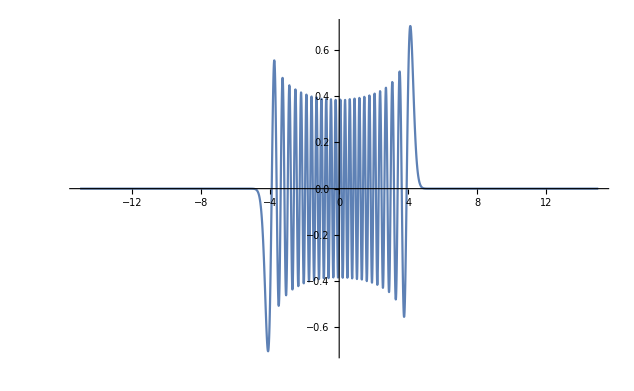

```mathematica
Plot[danh1d[[2]][[1]][[2]][[50]],{x,-15,15},PlotRange->All]
```

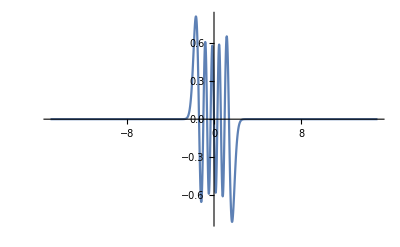

```mathematica
Plot[danh1d[[2]][[1]][[2]][[10]],{x,-15,15},PlotRange->All]
```

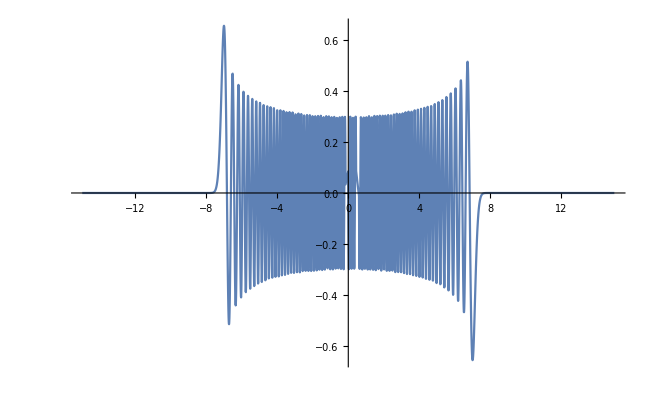

```mathematica
Plot[danh1d[[2]][[1]][[2]][[150]],{x,-15,15},PlotRange->All]
```

```mathematica
(*Vibrational Hamiltonian in normal mode coordinates is -1/2Laplcian[q,2] + 1/2omega^2q^2*)
VD[1,1,x]
```

{14.6 x^2,17.21 x^2,23.03 x^2}

```mathematica
(*Therefore the normal mode potential quadratic coefficient can be converted into omega_0 by multiplying by 2 and square rooting*)
(*Hamiltonian*)
ℒalld[[1]][[1]]
(*Quadratic potential coefficient*)
Sqrt[2ℒalld[[1]][[1]][[1]][[1]]]/2
(*First eigenfunction zero point omega_0/2 for comparison - same:*)
danh1d[[2]][[1]][[1]][[{1,2,3,4,100}]]
```

14.6 x^2 u[x]-u''[x]/2

2.70185

{2.93343,8.80028,14.6671,20.534,583.752}

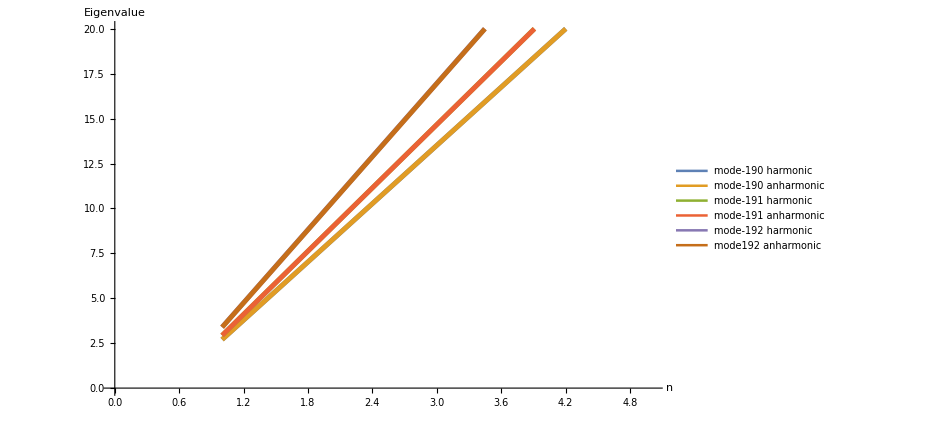

```mathematica
plotstuff={PlotStyle->Thickness[0.005],PlotLegends->Placed[{"mode-190 harmonic","mode-190 anharmonic","mode-191 harmonic","mode-191 anharmonic","mode-192 harmonic","mode192 anharmonic"},{0.5,0.8}],PlotRange->{{0,5},{0,20}},ImageSize->700,AxesLabel->{"n","Eigenvalue"}};
evals=Table[Table[danh1d[[mode]][[i]][[1]],{i,1,2}],{mode,1,3}];
evalsflat=Partition[Flatten[evals],250];
ListLinePlot[evalsflat,Evaluate@plotstuff]
```

```mathematica
Table[evalsflat[[i]][[1]],{i,1,6}]//TableForm
```

2.70185
2.70147
2.93343
2.93343
3.39338
3.3882